# Liver slices MFA

```mathematica
<<NilssonLab`MetabolicNetwork`
<<NilssonLab`ExtremePathways`
<<NilssonLab`AtomMap`
<<NilssonLab`EMUTracing`
<<NilssonLab`Visualization`
```

```mathematica
<<NilssonLab`OpenFLUX`
```

```mathematica
<<NilssonLab`IsotopeDistributions`
```

```mathematica
<<NilssonLab`GAMSFluxEstimation`
```

```mathematica
OpenDBConnection[]
```

## Set paths

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]]
```

C:\code\liver-flux-models\Models\liverModel_2_openFluxExport

```mathematica
patientId="L002";
```

```mathematica
experimentId="Human_liver_"<>patientId
```

Human_liver_L002

```mathematica
modelId="liver-model-working"
```

liver-model-working

```mathematica
lcmsDataDir="C:\\Users\\rolnil\\Linköpings universitet\\13C MFA - Documents\\Lever snitt ex vivo\\lcms-data";
```

## Import model

### Import from OpenFLUX format

We only keep the network model from OpenFLUX. (Targets are set from data)

```mathematica
net=First@OpenFLUXImport["liver-model_openflux.txt"];
```

Boundary network

```mathematica
bnet=BoundaryNetwork[net]
```

<BoundaryNetwork, 36 boundary fluxes>

### Check against network from database

```mathematica
dbNet=NetworkFromDB[modelId];
```

```mathematica
TrueQ[net==dbNet]
```

True

### Get atom map from database

All atom transitions for reactions in model

```mathematica
atomMap=AtomMapsFromDB[net,{"C"}];
atomMap=RenumberAtoms[RemoveUnreachable[net,atomMap]];
Length[atomMap]
```

90

Consistency check. Missing data for cofactors is okay at this stage as long as they are removed below.

```mathematica
CheckAtomMap[atomMap]
```

{}

Create boundary atom maps (only needed for uptake reactions!)

```mathematica
bmap=BoundaryAtomMaps[net,atomMap];
bmap//Length
```

36

Reactions without atom maps

```mathematica
Extract[Reactions[net],Position[AtomList/@atomMap,{}]]
```

{<Reaction ADK1>,<Reaction ATPS4m>,<Reaction ATPtm(rev)>,<Reaction CELLWORK>,<Reaction CRNtim>,<Reaction CYOOm>,<Reaction CYOR-u10m>,<Reaction H2Oter>,<Reaction H2Otm(rev)>,<Reaction Htm2(rev)>,<Reaction NADH2-u10m>,<Reaction NADH_REDOX>,<Reaction NDPK1>,<Reaction NH4tm(rev)>,<Reaction O2tm>,<Reaction PIt2m>,<Reaction PIter>,<Reaction PPA>}

### Symmetry

```mathematica
symmetry=GetSymmetryMap[atomMap]
```

{fum→{{1,2},{3,4}},succ→{{1,2},{3,4}}}

## Import LCMS data

### From peak area data

Import peak areas. We do not normalize at this step since peak areas are needed for uptake/release measurements

```mathematica
{measuredMetIds,sampleIds,measuredMIDs}=ImportMIDTable[FileNameJoin[{lcmsDataDir,"L002",experimentId<>"_peakareas_ambiguous_met.tsv"}]];
```

```mathematica
measuredMetIds
```

{{glc-D},{ala-L},{arg-L},{asn-L},{asp-L},{Lcystin},{gln-L},{his-L},{leu-L},{ile-L},{lys-L},{met-L},{phe-L},{pro-L},{ser-L},{thr-L},{trp-L},{tyr-L},{val-L},{mal-L},{f6p,g1p,g6p},{r5p},{udpg},{creat},{orn},{citr-L},{gudac},{glyc3p},{akg},{succ},{glu-L},{gly}}

### Targets

Define targets from measured metabolites present in the model

```mathematica
targets=Cases[MetaboliteEMUs[atomMap],EMU[Metabolite[Alternatives@@Flatten[measuredMetIds],__],_]]
```

{<akg_c{(12345)}>,<akg_m{(12345)}>,<ala-L_c{(123)}>,<arg-L_c{(123456)}>,<asp-L_c{(1234)}>,<asp-L_m{(1234)}>,<citr-L_c{(123456)}>,<citr-L_m{(123456)}>,<f6p_c{(123456)}>,<g1p_r{(123456)}>,<g6p_c{(123456)}>,<g6p_r{(123456)}>,<glc-D_c{(123456)}>,<glc-D_r{(123456)}>,<gln-L_c{(12345)}>,<gln-L_m{(12345)}>,<glu-L_c{(12345)}>,<glu-L_m{(12345)}>,<gly_c{(12)}>,<glyc3p_c{(123)}>,<mal-L_c{(1234)}>,<mal-L_m{(1234)}>,<orn_c{(12345)}>,<orn_m{(12345)}>,<ser-L_c{(123)}>,<succ_m{(1234)}>}

Drop any measured metabolites not in the model

```mathematica
Complement[Flatten[measuredMetIds],MetaboliteID/@Metabolite/@targets]
```

{asn-L,creat,gudac,his-L,ile-L,Lcystin,leu-L,lys-L,met-L,phe-L,pro-L,r5p,thr-L,trp-L,tyr-L,udpg,val-L}

```mathematica
Block[{ix},
ix=DeleteDuplicates[
First/@Position[measuredMetIds,Alternatives@@(MetaboliteID/@Metabolite/@targets)]];
measuredMIDs=measuredMIDs⟦ix⟧;
measuredMetIds=measuredMetIds⟦ix⟧;]
```

```mathematica
Length[measuredMetIds]
```

15

List of unique names for measurements, for use with GAMS

```mathematica
measuredMetNames=Map[ListToString[#,"__"]&,measuredMetIds]
```

{glc-D,ala-L,arg-L,asp-L,gln-L,ser-L,mal-L,f6p__g1p__g6p,orn,citr-L,glyc3p,akg,succ,glu-L,gly}

### EMU mixing matrix

Create (measurements x targets) mixing matrix

```mathematica
emuMixing=SparseArray[
Join@@Table[
Thread[Rule[
Thread[{i,Flatten[Position[targets,EMU[Metabolite[Alternatives@@measuredMetIds⟦i⟧,_,_],_]]]}],
1]],
{i,Length[measuredMetIds]}],
{Length[measuredMetIds],Length[targets]}]
```

SparseArray[<26>, {15, 26}]

Normalize rows to 1

```mathematica
emuMixing=SparseArray[emuMixing/(Total/@emuMixing)];
```

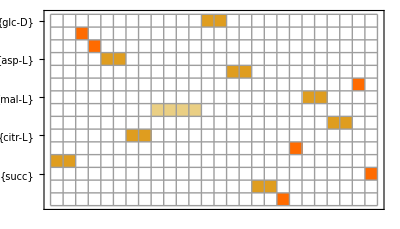

```mathematica
MatrixPlot[emuMixing,
FrameTicks->{Transpose[{Range[Length[measuredMetIds]],measuredMetIds}],None},Mesh->True]
```

List of measurement-target mappings

```mathematica
TableForm[Replace[
NonZeroIndices[emuMixing],
{i_,j_}:>{measuredMetNames⟦i⟧,targets⟦j⟧},{1}]]
```

glc-D | <glc-D_c{(123456)}>
glc-D | <glc-D_r{(123456)}>
ala-L | <ala-L_c{(123)}>
arg-L | <arg-L_c{(123456)}>
asp-L | <asp-L_c{(1234)}>
asp-L | <asp-L_m{(1234)}>
gln-L | <gln-L_c{(12345)}>
gln-L | <gln-L_m{(12345)}>
ser-L | <ser-L_c{(123)}>
mal-L | <mal-L_c{(1234)}>
mal-L | <mal-L_m{(1234)}>
f6p__g1p__g6p | <f6p_c{(123456)}>
f6p__g1p__g6p | <g1p_r{(123456)}>
f6p__g1p__g6p | <g6p_c{(123456)}>
f6p__g1p__g6p | <g6p_r{(123456)}>
orn | <orn_c{(12345)}>
orn | <orn_m{(12345)}>
citr-L | <citr-L_c{(123456)}>
citr-L | <citr-L_m{(123456)}>
glyc3p | <glyc3p_c{(123)}>
akg | <akg_c{(12345)}>
akg | <akg_m{(12345)}>
succ | <succ_m{(1234)}>
glu-L | <glu-L_c{(12345)}>
glu-L | <glu-L_m{(12345)}>
gly | <gly_c{(12)}>

### Sample annotations

For QC checks

Import as a rule table

```mathematica
sampleInfo=Import[
FileNameJoin[{lcmsDataDir,patientId,experimentId<>"_sampleinfo.tsv"}]];
sampleInfoFactors=Rest[First[sampleInfo]];
sampleInfo=Rest[sampleInfo ];
```

```mathematica
sampleInfo=Replace[sampleIds,Map[Rule[First[#],Rest[#]]&,sampleInfo],{1}]
```

{{tissue slice 0h,tissue extract,,L002,,human},{tissue slice 0h,tissue extract,,L002,,human},{tissue slice 0h,tissue extract,,L002,,human},{fresh tissue,tissue extract,,L002,,human},{fresh tissue,tissue extract,,L002,,human},{fresh tissue,tissue extract,,L002,,human},{tissue slice 2h,tissue extract,13C,L002,,human},{tissue slice 2h,tissue extract,13C,L002,,human},{tissue slice 2h,tissue extract,13C,L002,,human},{tissue slice 2h,tissue extract,12C,L002,,human},{tissue slice 2h,tissue extract,12C,L002,,human},{tissue slice 2h,tissue extract,12C,L002,,human},{tissue slice 24h,tissue extract,13C,L002,1,human},{tissue slice 24h,tissue extract,13C,L002,,human},{tissue slice 24h,tissue extract,13C,L002,,human},{tissue slice 24h,tissue extract,12C,L002,,human},{tissue slice 24h,tissue extract,12C,L002,,human},{tissue slice 24h,tissue extract,12C,L002,,human},{spent medium 2h,medium,13C,L002,,human},{spent medium 2h,medium,13C,L002,,human},{spent medium 2h,medium,13C,L002,,human},{spent medium 2h,medium,12C,L002,,human},{spent medium 2h,medium,12C,L002,,human},{spent medium 2h,medium,12C,L002,,human},{spent medium 24h,medium,13C,L002,1,human},{spent medium 24h,medium,13C,L002,,human},{spent medium 24h,medium,13C,L002,,human},{spent medium 24h,medium,12C,L002,,human},{spent medium 24h,medium,12C,L002,,human},{spent medium 24h,medium,12C,L002,,human},{fresh medium 0h,medium,13C,L002,,human},{fresh medium 24h,medium,13C,L002,,human},{fresh medium 24h,medium,13C,L002,,human},{fresh medium 24h,medium,13C,L002,,human},{fresh medium 0h,medium,12C,L002,,human},{fresh medium 24h,medium,12C,L002,,human},{fresh medium 24h,medium,12C,L002,,human},{fresh medium 24h,medium,12C,L002,,human},{,plasma,,L002,,human}}

Remove failed QC samples

```mathematica
Extract[sampleIds,Position[sampleInfo,{_,_,_,_,1,_}]]
```

{H_CE_LS_L_1,H_MS_LS_L_1}

```mathematica
Extract[sampleIds,Position[sampleInfo,{"fresh medium 24h",_,"12C",_,Except[1],_}]]//TableForm
```

H_MS_U_FM24h_1
H_MS_U_FM24h_2
H_MS_U_FM24h_3

## Uptake/release data

### Concentration estimates from medium fold changes

This reflects net balance, not directional fluxes.

Fresh medium concentrations (M)

```mathematica
initConc=Rest[Import["C:\\Users\\rolnil\\Linköpings universitet\\13C MFA - Documents\\Lever snitt ex vivo\\medium-concentrations\\williams_E.txt","TSV"]];
initConc=Cases[initConc,{Alternatives@@(MetaboliteID/@InputMetabolites[net]),_}];
{measuredBoundaryIds,initConc}=Transpose[initConc];
measuredBoundaryIds=Partition[measuredBoundaryIds,1];
```

Fold changes fresh (incubated) medium, paired

```mathematica
Extract[sampleIds,
Position[sampleInfo,{"fresh medium 24h",_,"12C",_,Except[1],_}]]
```

{H_MS_U_FM24h_1,H_MS_U_FM24h_2,H_MS_U_FM24h_3}

```mathematica
mediumFoldchange=Block[{metIndex,freshIndex,spentIndex},
metIndex=ReindexList[measuredBoundaryIds,measuredMetIds];
freshIndex=Flatten[Position[sampleInfo,{"fresh medium 24h",_,"12C",_,Except[1],_}]];
spentIndex=Flatten[Position[sampleInfo,{"spent medium 24h",_,"12C",_,Except[1],_}]];
Map[First,measuredMIDs⟦metIndex,spentIndex,1⟧,{2}]/Map[First,measuredMIDs⟦metIndex,freshIndex,1⟧,{2}]];
```

```mathematica
TableForm[mediumFoldchange,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | 0.66969 | 0.666832 | 0.656659
{arg-L} | 0.644172 | 0.902525 | 1.27053
{asp-L} | 0.677637 | 0.626805 | 0.710851
{gln-L} | 0.750615 | 0.676972 | 0.715755
{gly} | 0.748682 | 0.672288 | 0.594964
{ser-L} | 0.687248 | 0.624775 | 0.588538
{glc-D} | 0.886057 | 0.835328 | 0.843241

Convert to concentration differences

```mathematica
mediumConcDiff=initConc*(mediumFoldchange-1);
```

In um

```mathematica
TableForm[mediumConcDiff*10^6,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | -333.614 | -336.5 | -346.774
{arg-L} | -84.3313 | -23.1015 | 64.1155
{asp-L} | -72.8541 | -84.342 | -65.3477
{gln-L} | -498.771 | -646.055 | -568.491
{gly} | -167.629 | -218.584 | -270.159
{ser-L} | -29.774 | -35.7214 | -39.1712
{glc-D} | -1264.77 | -1827.86 | -1740.02

### As mean +/- std dev

```mathematica
mediumConcDiffMean=Mean/@mediumConcDiff;
```

```mathematica
mediumConcDiffSD=StandardDeviation/@mediumConcDiff;
```

```mathematica
TableForm[Transpose[{mediumConcDiffMean,mediumConcDiffSD}]*10^6,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | -338.962 | 6.91727
{arg-L} | -14.4391 | 74.6016
{asp-L} | -74.1813 | 9.56644
{gln-L} | -571.105 | 73.6771
{gly} | -218.79 | 51.2652
{ser-L} | -34.8888 | 4.75361
{glc-D} | -1610.88 | 302.944

### Add concentrations from clinical chemistry

Add lactate estimate (rough)

```mathematica
AppendTo[measuredBoundaryIds,{"lac-L"}];
AppendTo[mediumConcDiffMean,Mean[{1.0,1.5}]*0.001];
AppendTo[mediumConcDiffSD,StandardDeviation[{1.0,1.5}]*0.001];
```

```mathematica
TableForm[Transpose[{mediumConcDiffMean,mediumConcDiffSD}]*10^6,TableHeadings->{measuredBoundaryIds,None}]
```

{ala-L} | -338.962 | 6.91727
{arg-L} | -14.4391 | 74.6016
{asp-L} | -74.1813 | 9.56644
{gln-L} | -571.105 | 73.6771
{gly} | -218.79 | 51.2652
{ser-L} | -34.8888 | 4.75361
{glc-D} | -1610.88 | 302.944
{lac-L} | 1250. | 353.553

### Calculate net uptake/release fluxes

Convert to fluxes (positive = release)

```mathematica
mediumVolume=0.0013;
cultureTime=24;
```

In nmol / h

```mathematica
TableForm[
Transpose[{mediumConcDiffMean,mediumConcDiffSD}]*mediumVolume/cultureTime*10^9,
TableHeadings->{measuredBoundaryIds,{"mean","stddev"}}]
```

| mean | stddev
{ala-L} | -18.3605 | 0.374686
{arg-L} | -0.782118 | 4.04092
{asp-L} | -4.01815 | 0.518182
{gln-L} | -30.9349 | 3.99084
{gly} | -11.8511 | 2.77687
{ser-L} | -1.88981 | 0.257487
{glc-D} | -87.2563 | 16.4095
{lac-L} | 67.7083 | 19.1508

Map uptake/release fluxes to EMU fluxes

```mathematica
Block[{rules},
measFluxNames=First/@measuredBoundaryIds;
rules=Join@@Table[
Join[
Cases[BoundaryMetabolites[bnet],Metabolite[m,"Input",_]:>{m,m<>"_IN",-1}],
Cases[BoundaryMetabolites[bnet],Metabolite[m,"Output",_]:>{m,m<>"_OUT",1}]],
{m,measFluxNames}];
measReactions=Union[rules⟦All,2⟧];
fluxMixing=SparseArray[
Thread[Rule[
Transpose[{
ReindexList[rules⟦All,1⟧,measFluxNames],
ReindexList[rules⟦All,2⟧,measReactions]}],
rules⟦All,3⟧]],
{Length[measFluxNames],Length[measReactions]}]]
```

SparseArray[<12>, {8, 12}]

### Calculate absolute release fluxes (TODO)

```mathematica
spentMediumMIDs=Block[{metIndex,freshIndex,spentIndex},
metIndex=ReindexList[measuredBoundaryIds,measuredMetIds];
freshIndex=Flatten[Position[sampleInfo,{"spent medium 24h",_,"13C",_,Except[1],_}]];
spentIndex=Flatten[Position[sampleInfo,{"spent medium 24h",_,"13C",_,Except[1],_}]];
metIndex]
```

{2,3,4,5,15,6,1,Missing}

## Characterize the flux space

### Min/max fluxes

Note that this works in the space of net fluxes and hence excludes type III pathways!
Reactions that cannot carry net flux may still be important to fit MIDs because of exchange fluxes.

It would probably be better to run this with the sink output fixed at a smaller value (100) to get numerically more well-behaved solutions

```mathematica
netFluxMinMax=FindViableReactions[net,Tolerance->10.^-6];
Dimensions[netFluxMinMax]
```

{90,2}

Convert to absolute flux states and remove duplicates

```mathematica
fluxMinMax=Union[Chop[Join[
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,1⟧}],
Table[FluxState[net,nf],{nf,netFluxMinMax⟦All,2⟧}]]]];
```

```mathematica
Length[fluxMinMax]
```

77

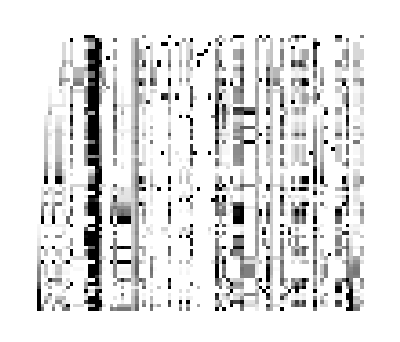

```mathematica
ArrayPlot[ForwardFlux/@fluxMinMax]
```

Generating random flux states from the min/max vectors, scaled to output = 100

```mathematica
RandomFluxState[n_]:=
Block[{f},
f=Mean[RandomChoice[fluxMinMax,n]]+0.001*Mean[fluxMinMax];
f/Total[PositivePart[MassBalance[net,f]]]*100]
```

### Check for blocked reactions

Reactions that cannot carry net flux in either direction.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,0}]//TableForm
```

<Reaction GHMT2r(rev)> | ser-L_c + thf_c <=> gly_c + h2o_c + mlthf_c | 0 | 0

Reactions that cannot carry net flux in the forward direction but in the reverse.

```mathematica
Cases[
Transpose[
{Reactions[net],Table[ReactionFormula[net,r],{r,Reactions[net]}],
Chop[Max/@Transpose[ForwardFlux/@fluxMinMax],0.001],
Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001]}],
{_,_,0,_?Positive}]
```

{}

Reversible reactions that cannot carry net flux in the reverse direction.

```mathematica
Table[
{r,ReactionFormula[net,r]},
{r,Extract[Reactions[net],
Intersection[
Position[Chop[Max/@Transpose[ReverseFlux/@fluxMinMax],0.001],0],
Position[ReversibleQ[Reactions[net]],True]]]}]
```

{{<Reaction ACONTm(rev)>,cit_m <=> icit_m},{<Reaction ASPTAm(rev)>,glu-L_m + oaa_m <=> akg_m + asp-L_m},{<Reaction ATPtm(rev)>,adp_c + atp_m <=> adp_m + atp_c},{<Reaction G6Pter(rev)>,g6p_c <=> g6p_r},{<Reaction GHMT2r(rev)>,ser-L_c + thf_c <=> gly_c + h2o_c + mlthf_c},{<Reaction GLUNm(rev)>,gln-L_m + h2o_m <=> glu-L_m + nh4_m},{<Reaction ICDHxm(rev)>,icit_m + nad_m <=> akg_m + co2_m + nadh_m},{<Reaction LDH_L(rev)>,h_c + nadh_c + pyr_c <=> lac-L_c + nad_c},{<Reaction MDHm(rev)>,mal-L_m + nad_m <=> h_m + nadh_m + oaa_m},{<Reaction PYRt2m(rev)>,pyr_c <=> pyr_m}}

Boundary fluxes that are never non-zero.

```mathematica
Pick[InputMetabolites[net],Chop[Max/@Transpose[BoundaryUptake/@fluxMinMax],.01],0]
```

{Metabolite[arg-L,Input,Boundary],Metabolite[energy,Input,Boundary],Metabolite[glyc,Input,Boundary],Metabolite[pi,Input,Boundary]}

```mathematica
Pick[OutputMetabolites[net],Chop[Max/@Transpose[BoundaryRelease/@fluxMinMax],0.01],0]
```

{Metabolite[pi,Output,Boundary]}

## EMU model

### EMU decomposition

Find EMU reactions (this takes some time)

```mathematica
emuReactions=EMUAlgorithm[net,atomMap,bmap,{"C"},targets,symmetry];
Length[emuReactions]
```

957

```mathematica
emuReactionNames=EMUFluxMap[net,"reactions"];
```

```mathematica
RandomSample[emuReactions,10]
```

{EMUReaction[129,<akg_m{(124)}>,<icit_m{(246)}>,1],EMUReaction[45,<accoa_m{(1)} x oaa_m{(2)}>,<cit_m{(26)}>,1],EMUReaction[112,<icit_m{(2)}>,<cit_m{(6)}>,1],EMUReaction[25,<cit_m{(136)}>,<icit_m{(246)}>,1],EMUReaction[104,<glu-L_c{(4)}>,<akg_c{(4)}>,1],EMUReaction[56,<g6p_r{(123456)}>,<glc-D_r{(123456)}>,1],EMUReaction[23,<cit_c{(13)}>,<oaa_c{(13)}>,1],EMUReaction[115,<oaa_c{(4)}>,<asp-L_c{(4)}>,1],EMUReaction[101,<ppcoa_m{(13)}>,<mmcoa-S_m{(14)}>,1],EMUReaction[120,<dhap_c{(123)} x g3p_c{(123)}>,<fdp_c{(123456)}>,1]}

Number of EMUs

```mathematica
emus=Union[Cases[emuReactions,EMUReaction[_,_,e_EMU,_]->e]];
emus//Length
```

487

```mathematica
SortBy[
Cases[emuReactions,
EMUReaction[i_,s_EMU,p:EMU[Metabolite["glc-D",__],_],_]:>{emuReactionNames⟦i⟧,s,p}],Last]//TableForm
```

glc-D_IN | <glc-D_i{(1)}> | <glc-D_c{(1)}>
GLCter_f | <glc-D_r{(1)}> | <glc-D_c{(1)}>
glc-D_IN | <glc-D_i{(2)}> | <glc-D_c{(2)}>
GLCter_f | <glc-D_r{(2)}> | <glc-D_c{(2)}>
glc-D_IN | <glc-D_i{(3)}> | <glc-D_c{(3)}>
GLCter_f | <glc-D_r{(3)}> | <glc-D_c{(3)}>
glc-D_IN | <glc-D_i{(4)}> | <glc-D_c{(4)}>
GLCter_f | <glc-D_r{(4)}> | <glc-D_c{(4)}>
glc-D_IN | <glc-D_i{(5)}> | <glc-D_c{(5)}>
GLCter_f | <glc-D_r{(5)}> | <glc-D_c{(5)}>
glc-D_IN | <glc-D_i{(6)}> | <glc-D_c{(6)}>
GLCter_f | <glc-D_r{(6)}> | <glc-D_c{(6)}>
glc-D_IN | <glc-D_i{(12)}> | <glc-D_c{(12)}>
GLCter_f | <glc-D_r{(12)}> | <glc-D_c{(12)}>
glc-D_IN | <glc-D_i{(23)}> | <glc-D_c{(23)}>
GLCter_f | <glc-D_r{(23)}> | <glc-D_c{(23)}>
glc-D_IN | <glc-D_i{(45)}> | <glc-D_c{(45)}>
GLCter_f | <glc-D_r{(45)}> | <glc-D_c{(45)}>
glc-D_IN | <glc-D_i{(56)}> | <glc-D_c{(56)}>
GLCter_f | <glc-D_r{(56)}> | <glc-D_c{(56)}>
glc-D_IN | <glc-D_i{(123)}> | <glc-D_c{(123)}>
GLCter_f | <glc-D_r{(123)}> | <glc-D_c{(123)}>
glc-D_IN | <glc-D_i{(456)}> | <glc-D_c{(456)}>
GLCter_f | <glc-D_r{(456)}> | <glc-D_c{(456)}>
glc-D_IN | <glc-D_i{(123456)}> | <glc-D_c{(123456)}>
GLCter_f | <glc-D_r{(123456)}> | <glc-D_c{(123456)}>
G6PPer_f | <g6p_r{(1)}> | <glc-D_r{(1)}>
G6PPer_f | <g6p_r{(2)}> | <glc-D_r{(2)}>
G6PPer_f | <g6p_r{(3)}> | <glc-D_r{(3)}>
G6PPer_f | <g6p_r{(4)}> | <glc-D_r{(4)}>
G6PPer_f | <g6p_r{(5)}> | <glc-D_r{(5)}>
G6PPer_f | <g6p_r{(6)}> | <glc-D_r{(6)}>
G6PPer_f | <g6p_r{(12)}> | <glc-D_r{(12)}>
G6PPer_f | <g6p_r{(23)}> | <glc-D_r{(23)}>
G6PPer_f | <g6p_r{(45)}> | <glc-D_r{(45)}>
G6PPer_f | <g6p_r{(56)}> | <glc-D_r{(56)}>
G6PPer_f | <g6p_r{(123)}> | <glc-D_r{(123)}>
G6PPer_f | <g6p_r{(456)}> | <glc-D_r{(456)}>
G6PPer_f | <g6p_r{(123456)}> | <glc-D_r{(123456)}>

Ensure targets are contained in EMUs

```mathematica
Complement[targets,emus]
```

{}

### Generate equation systems

```mathematica
emuEq=EMUSystem[emuReactions,NumberOfFluxes[EMUFluxMap[net]]];
```

```mathematica
TableForm[emuEq,TableHeadings->Automatic]
```

1 | <EMUEquation (1), 211 internals, 39 substrates, 0 condensations >
2 | <EMUEquation (2), 146 internals, 25 substrates, 6 condensations >
3 | <EMUEquation (3), 78 internals, 13 substrates, 5 condensations >
4 | <EMUEquation (4), 24 internals, 2 substrates, 4 condensations >
5 | <EMUEquation (5), 15 internals, 3 substrates, 2 condensations >
6 | <EMUEquation (6), 13 internals, 4 substrates, 2 condensations >

### Specify input isotopomers (tracers)

List the input metabolites that have atom information; for these the isotope distributions must be specified.

```mathematica
substrateDist=ImportMixtureID["substrate-distributions.txt"]
```

{2mop_i→NaturalIsotopomerDistribution[{4},{0.98}],ac_i→NaturalIsotopomerDistribution[{2},{0.0107}],ala-L_i→NaturalIsotopomerDistribution[{3},{0.98}],arg-L_i→NaturalIsotopomerDistribution[{6},{0.98}],asp-L_i→NaturalIsotopomerDistribution[{4},{0.98}],co2_i→NaturalIsotopomerDistribution[{1},{0.0107}],glc-D_i→NaturalIsotopomerDistribution[{6},{0.98}],gln-L_i→NaturalIsotopomerDistribution[{5},{0.98}],glucys_i→NaturalIsotopomerDistribution[{8},{0.0107}],gly_i→NaturalIsotopomerDistribution[{2},{0.98}],glyc_i→NaturalIsotopomerDistribution[{3},{0.0107}],glycogen_i→NaturalIsotopomerDistribution[{6},{0.0107}],prot_ala_i→NaturalIsotopomerDistribution[{3},{0.0107}],prot_arg_i→NaturalIsotopomerDistribution[{6},{0.0107}],ser-L_i→NaturalIsotopomerDistribution[{3},{0.98}]}

Calculate MIDs for network substrate EMUs

```mathematica
irList=Table[
Rule[e,Total[Table[
PDF[MarginalizeToMID[
FragmentIsotopomerDistribution[
MetaboliteShortName[Metabolite[e]]/.substrateDist,a]],
x],
{a,AtomNumbers[e]},{x,Tuples[Map[Range[0,Length[#]]&,a]]}]]],
{e,Flatten[SubstrateEMUs/@emuEq]}];
```

### Check: simulate steady-state mass isotopomer data

```mathematica
emuSol=EMUSimulate[emuEq,irList,EMUFluxMap[net][RandomFluxState[10]]]
```

<EMUSolution, 6 subsystems>

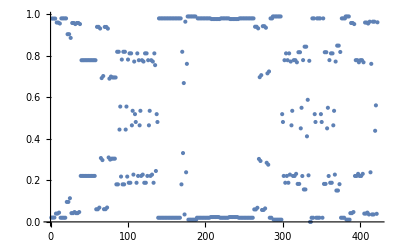
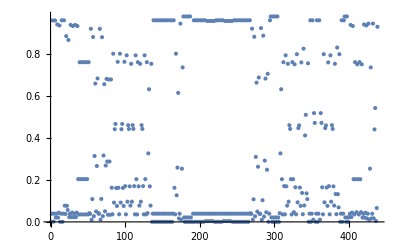
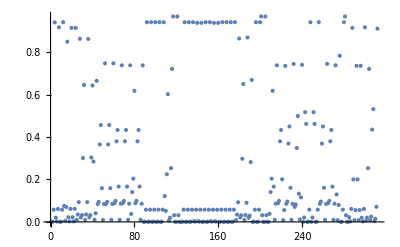
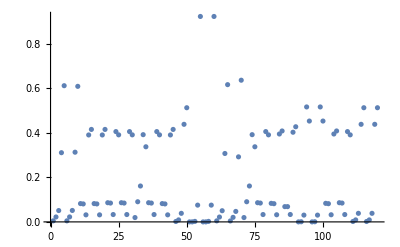
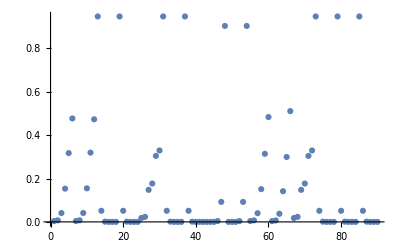
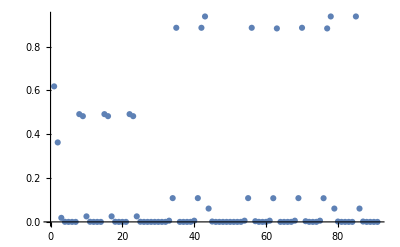

```mathematica
Table[
ListPlot[Flatten[InternalMIDs[emuSol,k]]],
{k,Length[emuEq]}]
```

```mathematica
Remove[emuSol]
```

## Analyze fluxes with GAMS, standard method

### Parameters

```mathematica
gamsModelName="liver-model";
```

```mathematica
gamsDir=FileNameJoin[{Directory[],"mathematica","gams"}]
```

C:\code\liver-flux-models\Models\liverModel_2_openFluxExport\mathematica\gams

```mathematica
If[!DirectoryQ[gamsDir],CreateDirectory[gamsDir]]
```

Here “experiments” referes to tracer settings (only one)

```mathematica
experiments={"experiment1"};
```

Smallest standard deviation allowed

```mathematica
minSD=0.01;
```

```mathematica
Directory[]
```

C:\code\liver-flux-models\Models\liverModel_2_openFluxExport

### Generate optimization model

MIDs to fit

```mathematica
midsToFit=Block[{sampleIndex},
sampleIndex=Flatten[Position[sampleInfo,{"tissue slice 24h",_,"13C",_,Except[1],_}]];
Map[First[MIDNormalize[#]]&,measuredMIDs⟦All,sampleIndex⟧,{2}]];
```

Export model file

```mathematica
GAMSExport[gamsDir,gamsModelName,
(* model *)
net,emuReactions,emuEq,{irList},
(* measured fluxes *)
measFluxNames,measReactions,mediumConcDiffMean*mediumVolume/cultureTime*10^9,mediumConcDiffSD*mediumVolume/cultureTime*10^9,fluxMixing,
(* measured MIDs *)
experiments,measuredMetNames,{Mean/@midsToFit},{Map[Max[StandardDeviation[#],minSD]&,midsToFit]},
(* targets *)
targets,emuMixing,
RandomFluxState[10]]
```

C:\code\liver-flux-models\Models\liverModel_2_openFluxExport\mathematica\gams\liver-model.gms

### Run GAMS

From command line ...

### Import GAMS solutions

#### Estimated mixing matrix

```mathematica
emuMixingGams=ImportGAMSEmuMixing[gamsDir,gamsModelName,measuredMetNames,targets]
```

SparseArray[<20>, {15, 26}]

```mathematica
Block[{ij,mix},
ij=NonZeroIndices[emuMixingGams];
Transpose[{measuredMetNames⟦ij⟦All,1⟧⟧,targets⟦ij⟦All,2⟧⟧,NonZeroElements[emuMixingGams]}]]//TableForm
```

glc-D | <glc-D_c{(123456)}> | 1.
ala-L | <ala-L_c{(123)}> | 1.
arg-L | <arg-L_c{(123456)}> | 1.
asp-L | <asp-L_c{(1234)}> | 0.432309
asp-L | <asp-L_m{(1234)}> | 0.567691
gln-L | <gln-L_c{(12345)}> | 0.925143
gln-L | <gln-L_m{(12345)}> | 0.0748566
ser-L | <ser-L_c{(123)}> | 1.
mal-L | <mal-L_m{(1234)}> | 1.
f6p__g1p__g6p | <f6p_c{(123456)}> | 0.245333
f6p__g1p__g6p | <g1p_r{(123456)}> | 0.754667
orn | <orn_c{(12345)}> | 0.5
orn | <orn_m{(12345)}> | 0.5
citr-L | <citr-L_c{(123456)}> | 0.5
citr-L | <citr-L_m{(123456)}> | 0.5
glyc3p | <glyc3p_c{(123)}> | 1.
akg | <akg_c{(12345)}> | 1.
succ | <succ_m{(1234)}> | 1.
glu-L | <glu-L_m{(12345)}> | 1.
gly | <gly_c{(12)}> | 1.

#### Simulated MIDs

For all EMUs in the model

```mathematica
midGams=ImportGAMSIsotopes[gamsDir,gamsModelName,experiments,emus];
```

Check dimensions

```mathematica
Length/@midGams⟦1⟧==(EMUSize/@emus)+1
```

True

Check specific MIDs

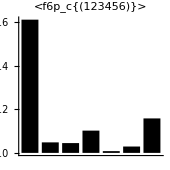
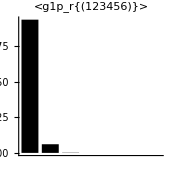
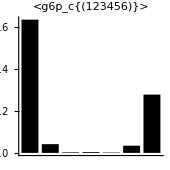
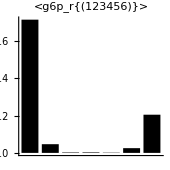
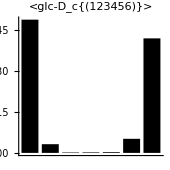
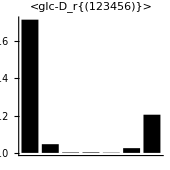

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["f6p"|"g6p"|"g1p"|"glc-D",_,_],{{{1,2,3,4,5,6}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

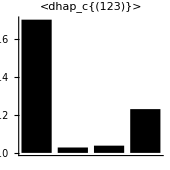
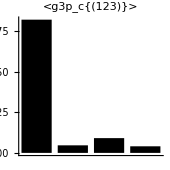
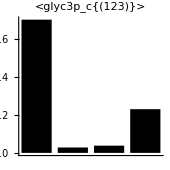

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["g3p"|"dhap"|"glyc3p",__],{{{1,2,3}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

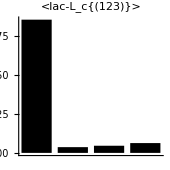

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["lac-L",_,_],{{{1,2,3}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

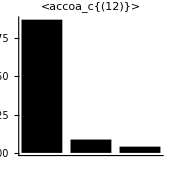
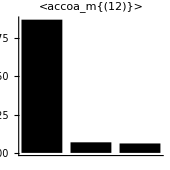

```mathematica
Block[{ix},
ix=Flatten[Position[emus,EMU[Metabolite["accoa",_,_],{{{1,2}}}]]];
Table[
SimpleBarChart[midGams⟦1,i⟧,PlotLabel->emus⟦i⟧,AspectRatio->1,ImageSize->170],
{i,ix}]]
```

#### Fitted MIDs

Recover fitted MIDs as mixing x target MIDs

```mathematica
fittedMIDs=Block[{ix,mix,mid},
mix=emuMixing;
mid=midGams⟦1,ReindexList[targets,emus]⟧;
Table[
ix=Flatten[Position[em,_?Positive]];
em⟦ix⟧.mid⟦ix⟧,
{em,mix}]];
```

Compare fitted MIDs (gray) with measured (black)

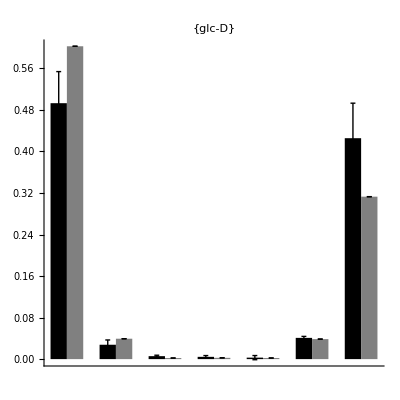
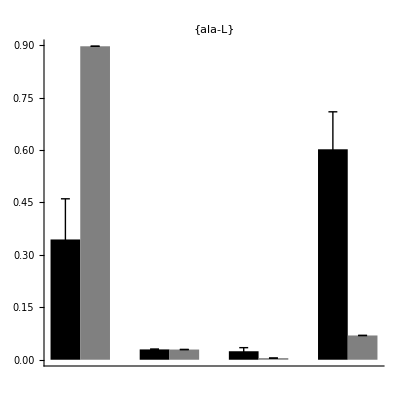
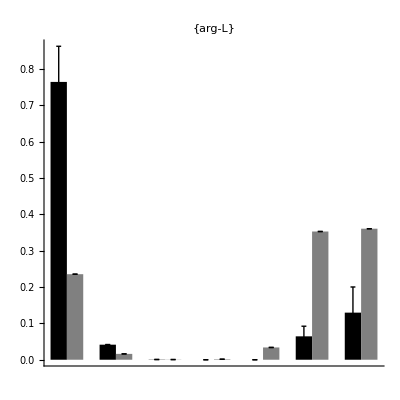
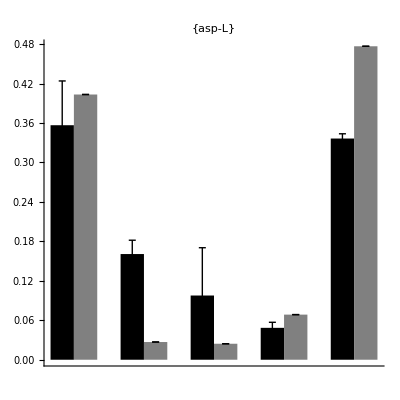
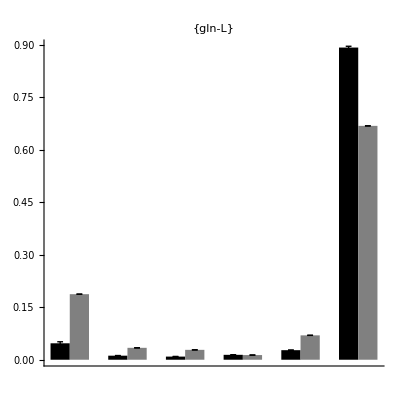
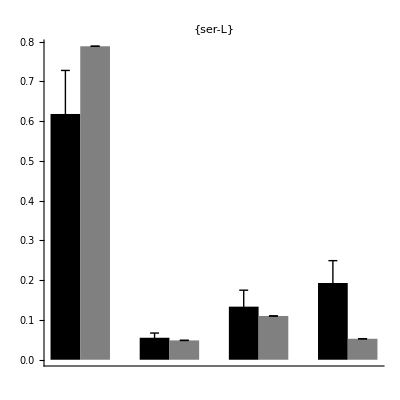
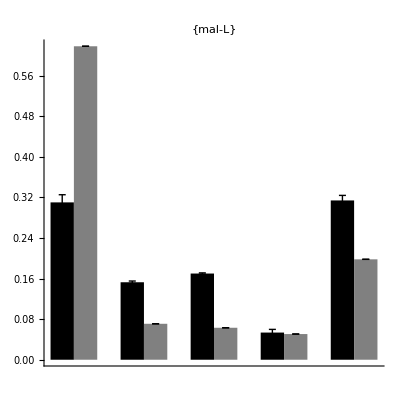
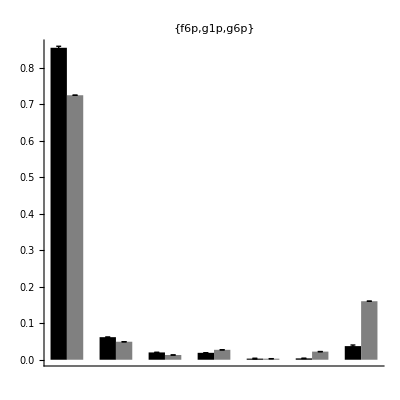

```mathematica
Table[
ErrorBarChart[
Transpose/@{midsToFit⟦i⟧,Table[fittedMIDs⟦i⟧,{3}]},
AspectRatio->1,PlotLabel->measuredMetIds⟦i⟧],
{i,Length[measuredMetIds]}]
```

Scatter plot of all fitted MIDs

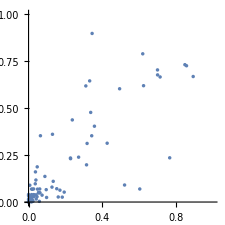

```mathematica
ListPlot[
Transpose[{Flatten[Mean/@midsToFit],Flatten[fittedMIDs]}],PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

#### Fluxes

```mathematica
fluxGams=ImportGAMSFluxes[gamsDir,gamsModelName,net,EMUFluxMap[net]]
```

<FluxState, 90 reactions, 36 b. exch>

```mathematica
TableForm[
Transpose[{ForwardFlux[fluxGams],ReverseFlux[fluxGams],NetFlux[fluxGams]}],
TableHeadings->{Reactions[net],{"fwd","rev","net"}}]
```

| fwd | rev | net
<Reaction 2AMACHYD> | 158.966 | 0. | 158.966
<Reaction ACITL> | 161.665 | 0. | 161.665
<Reaction ACOAHi> | 0.001 | 0. | 0.001
<Reaction ACONTm(rev)> | 809.531 | 711.447 | 98.0836
<Reaction ACRNtm> | 161.666 | 0. | 161.666
<Reaction ACS> | 0.002 | 0. | 0.002
<Reaction ADK1> | 8.54817 | 0. | 8.54817
<Reaction AKGDm(rev)> | 310.454 | 298.238 | 12.2165
<Reaction AKGtm(rev)> | 0.001 | 85.8691 | -85.8681
<Reaction ALATA_L> | 247.548 | 0. | 247.548
<Reaction ARGN> | 8.54617 | 0. | 8.54617
<Reaction ARGSL> | 8.54617 | 0. | 8.54617
<Reaction ARGSS> | 8.54617 | 0. | 8.54617
<Reaction ASPTA(rev)> | 0.001 | 4.54855 | -4.54755
<Reaction ASPTAm(rev)> | 0.002 | 0.001 | 0.001
<Reaction ASPtm> | 0.001 | 0. | 0.001
<Reaction ATPS4m> | 591.197 | 0. | 591.197
<Reaction ATPtm(rev)> | 347.337 | 0.001 | 347.336
<Reaction CBPSam> | 8.54617 | 0. | 8.54617
<Reaction CELLWORK> | 0.001 | 0. | 0.001
<Reaction CITtm> | 161.665 | 0. | 161.665
<Reaction CO2tm(rev)> | 10000. | 9960.85 | 39.1484
<Reaction CRNtim> | 161.666 | 0. | 161.666
<Reaction CSm> | 259.749 | 0. | 259.749
<Reaction CSNATm> | 161.666 | 0. | 161.666
<Reaction CSNATr> | 161.666 | 0. | 161.666
<Reaction CYOOm> | 120.683 | 0. | 120.683
<Reaction CYOR-u10m> | 241.366 | 0. | 241.366
<Reaction ENO(rev)> | 0.00663902 | 157.122 | -157.115
<Reaction FBA(rev)> | 10000. | 9999.98 | 0.024633
<Reaction FBP> | 0.0208379 | 0. | 0.0208379
<Reaction FUMm> | 20.7636 | 0. | 20.7636
<Reaction FUMtm> | 8.54617 | 0. | 8.54617
<Reaction G3PD1> | 0.0327218 | 0. | 0.0327218
<Reaction G6PPer> | 0.0185206 | 0. | 0.0185206
<Reaction G6Pter(rev)> | 0.0490283 | 0.0480283 | 0.001
<Reaction GAPD(rev)> | 10000. | 9999.98 | 0.0165443
<Reaction GHMT2r(rev)> | 7.24025 | 7.24025 | 0.
<Reaction GLCter> | 0.0175206 | 0. | 0.0175206
<Reaction GLNtm> | 37.5231 | 0. | 37.5231
<Reaction GLUDxm(rev)> | 0.001 | 0.001 | 0.
<Reaction GLUNm(rev)> | 9164.45 | 9126.93 | 37.5231
<Reaction GLUt2m(rev)> | 115.497 | 153.019 | -37.5221
<Reaction GLYCOGEN_BREAKer> | 0.0175206 | 0. | 0.0175206
<Reaction GLYCPH> | 0.0337218 | 0. | 0.0337218
<Reaction GLYK> | 0.001 | 0. | 0.001
<Reaction GTHS> | 11.4029 | 0. | 11.4029
<Reaction H2Oter> | 0.0185206 | 0. | 0.0185206
<Reaction H2Otm(rev)> | 0.00113122 | 266.996 | -266.995
<Reaction HCO3Em> | 247.532 | 0. | 247.532
<Reaction HEX1> | 0.025633 | 0. | 0.025633
<Reaction Htm2(rev)> | 4.47041 | 32.146 | -27.6756
<Reaction ICDHxm(rev)> | 818.823 | 720.739 | 98.0836
<Reaction LDH_L(rev)> | 69.4485 | 0.001 | 69.4475
<Reaction MALtm> | 0.001 | 0. | 0.001
<Reaction MDH> | 0.001 | 0. | 0.001
<Reaction MDHm(rev)> | 20.7656 | 0.001 | 20.7646
<Reaction MMEm> | 0.001 | 0. | 0.001
<Reaction MMMm> | 0.001 | 0. | 0.001
<Reaction MMSAD1m> | 0.001 | 0. | 0.001
<Reaction NADH2-u10m> | 229.148 | 0. | 229.148
<Reaction NADH_REDOX> | 87.6672 | 0. | 87.6672
<Reaction NDPK1> | 157.116 | 0. | 157.116
<Reaction NH4tm(rev)> | 0.001 | 28.9779 | -28.9769
<Reaction O2tm> | 120.683 | 0. | 120.683
<Reaction OCBTm> | 8.54617 | 0. | 8.54617
<Reaction ORNt4m> | 8.54617 | 0. | 8.54617
<Reaction PCm> | 238.985 | 0. | 238.985
<Reaction PDHm> | 98.0826 | 0. | 98.0826
<Reaction PEPCK> | 157.116 | 0. | 157.116
<Reaction PFK> | 0.0454709 | 0. | 0.0454709
<Reaction PGCD> | 157.132 | 0. | 157.132
<Reaction PGI(rev)> | 0.025633 | 0.001 | 0.024633
<Reaction PGK(rev)> | 10000. | 9999.98 | 0.0165443
<Reaction PGM(rev)> | 0.001 | 157.116 | -157.115
<Reaction PGMTer> | 0.0175206 | 0. | 0.0175206
<Reaction PIt2m> | 347.336 | 0. | 347.336
<Reaction PIter> | 0.001 | 0. | 0.001
<Reaction PPA> | 8.54817 | 0. | 8.54817
<Reaction PPCOACm> | 0.001 | 0. | 0.001
<Reaction PROTDEG_ALA> | 229.295 | 0. | 229.295
<Reaction PROTDEG_ARG> | 2.47847 | 0. | 2.47847
<Reaction PSERT> | 157.132 | 0. | 157.132
<Reaction PSP_L> | 157.132 | 0. | 157.132
<Reaction PYK> | 0.001 | 0. | 0.001
<Reaction PYRt2m(rev)> | 337.068 | 0.001 | 337.067
<Reaction SERHL> | 158.966 | 0. | 158.966
<Reaction SUCD1m> | 12.2175 | 0. | 12.2175
<Reaction SUCOASm> | 12.2175 | 0. | 12.2175
<Reaction TPI(rev)> | 0.001 | 0.00908873 | -0.00808873

```mathematica
MetaboliteProducers[net,Metabolite["glc-D","Cytosol","Uptake"]]
```

{{<Reaction GLCter>,1}}

Boundary fluxes

```mathematica
TableForm[
BoundaryFlux[fluxGams],
TableHeadings->{BoundaryFluxNames[bnet],None}]
```

2mop_IN | 0.001
ac_IN | 0.001
ala-L_IN | 18.2525
arg-L_IN | 7.3634
asp-L_IN | 10000.
co2_IN | 9882.03
energy_IN | 0.001
glc-D_IN | 0.00811245
gln-L_IN | 37.5231
glucys_IN | 11.4029
gly_IN | 11.4029
glyc_IN | 0.001
glycogen_IN | 0.0175206
h2o_IN | 64.4223
h_IN | 0.001
nh4_IN | 0.942934
o2_IN | 120.683
pi_IN | 0.001
prot_ala_IN | 229.295
prot_arg_IN | 2.47847
ser-L_IN | 1.83547
arg-L_OUT | 9.84187
asp-L_OUT | 9996.
co2_OUT | 10000.
energy_OUT | 0.002
glc-D_OUT | 0.001
glu-L_OUT | 123.39
glyc_OUT | 0.0337218
gthrd_OUT | 11.4029
h2o_OUT | 0.001
h_OUT | 176.23
lac-L_OUT | 69.4475
nh4_OUT | 188.886
pi_OUT | 0.001
ser-L_OUT | 0.001
urea_OUT | 8.54617

Fitted flux measurements

```mathematica
Block[{ix},
ix=ReindexList[measReactions,BoundaryFluxNames[bnet]];
TableForm[
Transpose[{fluxMixing.BoundaryFlux[fluxGams]⟦ix⟧,mediumConcDiffMean*mediumVolume/cultureTime*10^9}],
TableHeadings->{measFluxNames,{"fitted","measured"}}]]
```

| fitted | measured
ala-L | -18.2525 | -18.3605
arg-L | 2.47847 | -0.782118
asp-L | -3.99762 | -4.01815
gln-L | -37.5231 | -30.9349
gly | -11.4029 | -11.8511
ser-L | -1.83447 | -1.88981
glc-D | -0.00711245 | -87.2563
lac-L | 69.4475 | 67.7083

```mathematica
,
```